```mathematica
<<Vilcretas`
```

VilCretas está disponible.

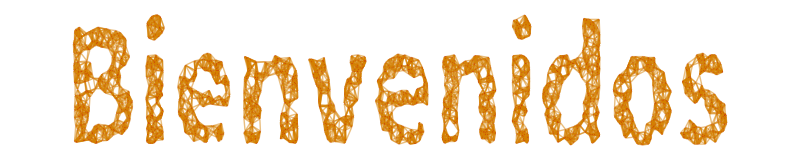

```mathematica
GrafoString["Bienvenidos"]
```

```mathematica
f=2^(j*n)(-12 n^(4j)-16 n^3-8 n^2+20n-5);
g=4^(12-2n);
```

```mathematica
?CompLimit
```

```mathematica
CompLimit[{f, g}, jvalor->100]
```

```mathematica
Table[j->Limit[f/g, n->Infinity],{j,-10,10}]
```

{-10→0,-9→0,-8→0,-7→0,-6→0,-5→0,-4→-∞,-3→-∞,-2→-∞,-1→-∞,0→-∞,1→-∞,2→-∞,3→-∞,4→-∞,5→-∞,6→-∞,7→-∞,8→-∞,9→-∞,10→-∞}

```mathematica
f=Sum[((1/2)^i+(i+1/2)^6+100)^3,{i,1,3n-1}];
```

```mathematica
Expand[f]
```

35430551813318191625/148635648-1/7 2^(3-9 n)-1087409/81 2^(-4-6 n)-488187622615971 2^(-11-3 n)+(1358828490091679 n)/453246976-65735/9 2^(-2-6 n) n-126894670895169 2^(-8-3 n) n-15175 2^(-2-6 n) n^2-131935024962027 2^(-8-3 n) n^2+(37492152453 n^3)/327680-2625 2^(1-6 n) n^3-22862597470965 2^(-6-3 n) n^3-23770718204445 2^(-7-3 n) n^4-5535 2^(-6 n) n^4-(7197860961 n^5)/4096-1215 2^(2-6 n) n^5-617873101137 2^(-3-3 n) n^5-729 2^(2-6 n) n^6-214138283229 2^(-3-3 n) n^6+(316918408383 n^7)/35840-15902663337 2^(-1-3 n) n^7-16534015245 2^(-3-3 n) n^8+(1145189745 n^9)/512-477411165 2^(-3 n) n^9-99379467 2^(-3 n) n^10-(2090157453 n^11)/640-4782969 2^(2-3 n) n^11-1594323 2^(1-3 n) n^12-(3269956473 n^13)/208+(1707519933 n^15)/20-(387420489 n^17)/4+(1162261467 n^19)/19

```mathematica
Limit[f/n^19, n->Infinity]
```

1162261467/19

```mathematica
f1[n_]:=f1[n-1]-f1[n-2]+f1[n-3]
f1[0]=4;f1[1]=7;
f1[2]=6;
f2[n_]:=Which[n==0,4,n==1,7,n==2,6,n>2,f2[n-1]-f2[n-2]+f2[n-3]]
f3[n_]:=Module[{g},g[i_,a_,ta_,tta_]:=Which[n==0,tta,n==1,ta,n==2,a,i==n,a-ta+tta,True,g[i+1,a-ta+tta,a,ta]];
g[3,6,7,4]]

f4[n_]:=Module[{i,s=0},For[i=1,i<=n,i++,s=s+i];
Which[n==0,4,n==1,7,n==2,6,n>2,f4[n-1]-f4[n-2]+f4[n-3]]]
```

```mathematica
PruebaADAGrafica[{f1,f2,f3,f4},20,5,1]
```

-Graphics-

```mathematica
opciones={n^4,n^2,5^n,(1/11)^n,11^n};

Table[i->Limit[((1/11)^(-n)-7 n^4+4 n^2+5^n)/i,n->Infinity],{i,opciones}]
```

{n^4→∞,n^2→∞,5^n→∞,11^-n→∞,11^n→1}

```mathematica
CompLimit[{(2 n^7+2 n^2)/(5 n^j+3 n^2+1),n^j}]
```

```mathematica
Limit[(n^3+(n^3+n-9160)/(6n)+9)/n^2, n->Infinity]
```

∞